```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

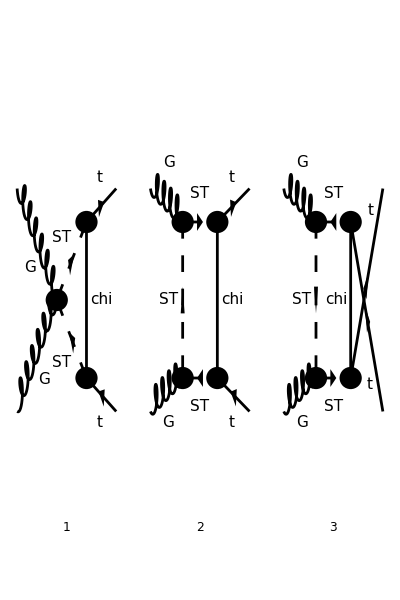

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
goodDiags=DiagramExtract[goodDiags,{4,10,11}];
(* goodDiags=DiagramExtract[goodDiags,{4}]; *)
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 400,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 3 Particles amplitudes

-gs^2 yDM^2 ((γ·q).(γ̄)^6 ((g^μν ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4))/((q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))+(k2^ν+2 q^ν) (k2^μ-p1^μ-p2^μ+2 q^μ) (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))+(k2^ν+2 q^ν) (k2^μ-p1^μ-p2^μ+2 q^μ) ((((γ·k2).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(((γ·p1).(γ̄)^6-(γ·k2).(γ̄)^6) (T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u-> 2 MT^2};
```

## Check Divergences

```mathematica
Table[{Cases2[ampEsimp2,PaVe][[i]],PaXEvaluateUV[Cases2[ampEsimp2,PaVe][[i]]]},{i,1,Length[Cases2[ampEsimp2,PaVe]]}]
```

(C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) | 0
D_1(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_1(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_2(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_3(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_00(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_00(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_11(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_11(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_13(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_13(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_22(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_002(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_002(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_003(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_003(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_111(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_111(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_113(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_113(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_122(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_122(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_123(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_123(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_133(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_133(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_222(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_222(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_223(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0)

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[Coefficient[ampEsimp2,deltaCTR]] (-1/(4 EpsilonUV));
FullSimplify[loopUV+ctUV]
```

0

```mathematica
PaVe[3,3,3,{0,u,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},PaVeAutoOrder->True,PaVeAutoReduce->True]
```

D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)

### Replace D - integrals by short names

```mathematica
PVsubs =Flatten[Table[PaVe[a,{0,b,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a],"_",ToString[b]]],{a,0,3},{b,{u,t}}]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,{0,b,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],"_",ToString[b]]],{a1,0,3},{a2,0,3},{b,{u,t}}]]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,a3,{0,b,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[a3],"_",ToString[b]]],{a1,0,3},{a2,0,3},{a3,0,3},{b,{u,t}}]]];
PVsubs = Join[PVsubs,{PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},c__]->C1,D0[0,MT^2,MT^2,0,t,s,mST^2,mST^2,mChi^2,mST^2]->D0}];
```

#### Check replacements

```mathematica
Table[{Cases2[ampEsimp2,PaVe][[i]],Cases2[ampEsimp2,PaVe][[i]]/.PVsubs},{i,1,Length[Cases2[ampEsimp2,PaVe]]}];
```

```mathematica
ampEsimp3=Simplify[ampEsimp2/.PVsubs];
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]]
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]]
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]]
allTerms=Sort[Join[spinorChains,singleGammas]];
```

{γ^ν,(γ̄)^6,γ^μ,γ·k2,γ·p1,γ·p2}

{γ^ν.(γ̄)^6,γ^μ.(γ̄)^6,(γ·k2).(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6}

{}

### Coefficients for each term

```mathematica
tensorTerms=Table[{allTerms[[i]],FullSimplify[Coefficient[ampEsimp3,allTerms[[i]]]]},{i,1,Length[allTerms]}]
```

((γ̄)^6 | 0
γ^μ | 0
γ^ν | 0
γ·k2 | 0
γ·p1 | 0
γ·p2 | 0
γ^μ.(γ̄)^6 | 2 ⅈ π^2 gs^2 yDM^2 ((T^Glu1 T^Glu2)_Col3Col4 ((2 D001_t+D00_t) k2^ν+2 (D002_t+D003_t) p2^ν+2 D003_t p1^ν)-(T^Glu2 T^Glu1)_Col3Col4 ((2 D001_u+D00_u) k2^ν+2 (D002_u+D003_u) p1^ν+2 D003_u p2^ν))
γ^ν.(γ̄)^6 | 2 ⅈ π^2 gs^2 yDM^2 ((T^Glu1 T^Glu2)_Col3Col4 ((2 D001_t+D00_t) k2^μ+p2^μ (2 (D002_t+D003_t)+D00_t)+(2 D003_t+D00_t) p1^μ)-(T^Glu2 T^Glu1)_Col3Col4 ((2 D001_u+D00_u) k2^μ+p1^μ (2 (D002_u+D003_u)+D00_u)+(2 D003_u+D00_u) p2^μ))
(γ·k2).(γ̄)^6 | ⅈ gs^2 π^2 yDM^2 (p1^μ k2^ν D1_t (T^Glu1 T^Glu2)_Col3Col4+p2^μ k2^ν D1_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D11_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D11_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ k2^ν D112_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ k2^ν D113_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ k2^ν D113_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D12_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D12_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p2^ν D12_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p2^ν D122_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p1^ν D123_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p2^ν D123_t (T^Glu1 T^Glu2)_Col3Col4+8 p2^μ p2^ν D123_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p1^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p1^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p1^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p1^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p2^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p2^ν D133_t (T^Glu1 T^Glu2)_Col3Col4-(p2^μ (2 p1^ν (D12_u+2 D123_u)+k2^ν (D1_u+2 (D11_u+2 D113_u+D13_u))+2 (p1^ν+p2^ν) (D13_u+2 D133_u))+p1^μ (k2^ν (D1_u+2 (D11_u+2 D112_u+2 D113_u+D12_u+D13_u))+2 (p2^ν (2 D123_u+D13_u+2 D133_u)+p1^ν (D12_u+2 D122_u+4 D123_u+D13_u+2 D133_u)))) (T^Glu2 T^Glu1)_Col3Col4+4 g^μν (D001_t (T^Glu1 T^Glu2)_Col3Col4-D001_u (T^Glu2 T^Glu1)_Col3Col4)+k2^μ ((k2^ν (D1_t+4 (D11_t+D111_t))+2 (p1^ν (2 D113_t+D13_t)+p2^ν (2 D112_t+2 D113_t+D12_t+D13_t))) (T^Glu1 T^Glu2)_Col3Col4-(k2^ν (D1_u+4 (D11_u+D111_u))+2 (p2^ν (2 D113_u+D13_u)+p1^ν (2 D112_u+2 D113_u+D12_u+D13_u))) (T^Glu2 T^Glu1)_Col3Col4))
(γ·p1).(γ̄)^6 | ⅈ gs^2 π^2 yDM^2 (4 p2^μ k2^ν D123_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ k2^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ k2^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p2^ν D223_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p1^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p2^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+8 p2^μ p2^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+p1^μ k2^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+p2^μ k2^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p1^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p1^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p1^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p1^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p2^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p2^ν D333_t (T^Glu1 T^Glu2)_Col3Col4-(D_0(0,MT^2,MT^2,0,u,s,mST^2,mST^2,mChi^2,mST^2) (p1^μ+p2^μ) k2^ν+p2^μ (k2^ν (2 D1_u+2 D12_u+4 D123_u+6 D13_u+4 D133_u+D2_u+2 D23_u+3 D3_u+2 D33_u)+2 p2^ν (D23_u+2 D233_u+D3_u+3 D33_u+2 D333_u)+2 p1^ν (D2_u+D22_u+2 D223_u+4 D23_u+4 D233_u+D3_u+3 D33_u+2 D333_u))+p1^μ (k2^ν (2 D1_u+6 D12_u+4 D122_u+8 D123_u+6 D13_u+4 D133_u+3 D2_u+2 D22_u+4 D23_u+3 D3_u+2 D33_u)+2 p2^ν (2 D223_u+3 D23_u+4 D233_u+D3_u+3 D33_u+2 D333_u)+2 p1^ν (D2_u+3 D22_u+2 D222_u+6 D223_u+6 D23_u+6 D233_u+D3_u+3 D33_u+2 D333_u))) (T^Glu2 T^Glu1)_Col3Col4+g^μν (-(C1-4 D003_t) (T^Glu1 T^Glu2)_Col3Col4-(C1+4 D00_u+4 D002_u+4 D003_u) (T^Glu2 T^Glu1)_Col3Col4)+k2^μ (2 (p1^ν (2 D133_t+D33_t)+p2^ν (2 D123_t+2 D133_t+D23_t+D33_t)) (T^Glu1 T^Glu2)_Col3Col4-2 (p2^ν (2 D123_u+2 D13_u+2 D133_u+D23_u+D3_u+D33_u)+p1^ν (2 D12_u+2 D122_u+4 D123_u+2 D13_u+2 D133_u+D2_u+D22_u+2 D23_u+D3_u+D33_u)) (T^Glu2 T^Glu1)_Col3Col4+k2^ν ((4 (D113_t+D13_t)+D3_t) (T^Glu1 T^Glu2)_Col3Col4-(D_0(0,MT^2,MT^2,0,u,s,mST^2,mST^2,mChi^2,mST^2)+4 D1_u+4 D11_u+4 D112_u+4 D113_u+4 D12_u+4 D13_u+D2_u+D3_u) (T^Glu2 T^Glu1)_Col3Col4)))
(γ·p2).(γ̄)^6 | ⅈ gs^2 π^2 yDM^2 (D0 p1^μ k2^ν (T^Glu1 T^Glu2)_Col3Col4+D0 p2^μ k2^ν (T^Glu1 T^Glu2)_Col3Col4+g^μν (C1+4 D00_t+4 D002_t+4 D003_t) (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D1_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D1_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D12_t (T^Glu1 T^Glu2)_Col3Col4+6 p2^μ k2^ν D12_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ k2^ν D122_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ k2^ν D123_t (T^Glu1 T^Glu2)_Col3Col4+8 p2^μ k2^ν D123_t (T^Glu1 T^Glu2)_Col3Col4+6 p1^μ k2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+6 p2^μ k2^ν D13_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ k2^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ k2^ν D133_t (T^Glu1 T^Glu2)_Col3Col4+p1^μ k2^ν D2_t (T^Glu1 T^Glu2)_Col3Col4+3 p2^μ k2^ν D2_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D2_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p2^ν D2_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D22_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D22_t (T^Glu1 T^Glu2)_Col3Col4+6 p2^μ p2^ν D22_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p2^ν D222_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p1^ν D223_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p2^ν D223_t (T^Glu1 T^Glu2)_Col3Col4+12 p2^μ p2^ν D223_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ k2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p1^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+6 p2^μ p1^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+8 p1^μ p2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+12 p2^μ p2^ν D23_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p1^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+8 p2^μ p1^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+8 p1^μ p2^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+12 p2^μ p2^ν D233_t (T^Glu1 T^Glu2)_Col3Col4+3 p1^μ k2^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+3 p2^μ k2^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p1^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p1^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ p2^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ p2^ν D3_t (T^Glu1 T^Glu2)_Col3Col4+2 p1^μ k2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+2 p2^μ k2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+6 p1^μ p1^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+6 p2^μ p1^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+6 p1^μ p2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+6 p2^μ p2^ν D33_t (T^Glu1 T^Glu2)_Col3Col4+k2^μ (k2^ν (D0+4 D1_t+4 D11_t+4 D112_t+4 D113_t+4 D12_t+4 D13_t+D2_t+D3_t)+2 p1^ν (2 D123_t+2 D13_t+2 D133_t+D23_t+D3_t+D33_t)+2 p2^ν (2 D12_t+2 D122_t+4 D123_t+2 D13_t+2 D133_t+D2_t+D22_t+2 D23_t+D3_t+D33_t)) (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p1^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p1^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+4 p1^μ p2^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+4 p2^μ p2^ν D333_t (T^Glu1 T^Glu2)_Col3Col4+(g^μν (C1-4 D003_u)-k2^μ (k2^ν (4 (D113_u+D13_u)+D3_u)+2 (p2^ν (2 D133_u+D33_u)+p1^ν (2 D123_u+2 D133_u+D23_u+D33_u)))-p2^μ (2 p1^ν (D23_u+2 D233_u)+k2^ν (2 D13_u+4 D133_u+D3_u+2 D33_u)+2 (p1^ν+p2^ν) (D33_u+2 D333_u))-p1^μ (k2^ν (4 D123_u+2 D13_u+4 D133_u+2 D23_u+D3_u+2 D33_u)+2 p2^ν (2 D233_u+D33_u+2 D333_u)+2 p1^ν (2 D223_u+D23_u+4 D233_u+D33_u+2 D333_u))) (T^Glu2 T^Glu1)_Col3Col4))